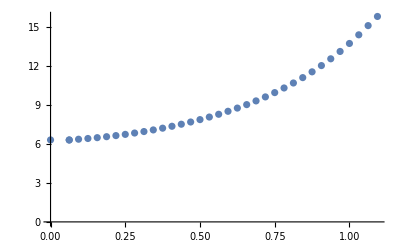

```mathematica
a={{0,6.313705},{0.062500,6.309771},{0.062500,6.309771},{0.093750,6.368520},{0.125000,6.424554},{0.156250,6.489058},{0.187500,6.563377},{0.218750,6.647642},{0.250000,6.741820},{0.281250,6.845929},{0.312500,6.960103},{0.343750,7.084594},{0.375000,7.219776},{0.406250,7.366142},{0.437500,7.524296},{0.468750,7.694947},{0.500000,7.878910},{0.531250,8.077097},{0.562500,8.290516},{0.593750,8.520270},{0.625000,8.767552},{0.656250,9.033655},{0.687500,9.319972},{0.718750,9.628014},{0.750000,9.959433},{0.781250,10.316059},{0.812500,10.699957},{0.843750,11.113503},{0.875000,11.559492},{0.906250,12.041271},{0.937500,12.562863},{0.968750,13.128994},{1.000000,13.744415},{1.031250,14.410556},{1.062500,15.120190},{1.093750,15.824833}};
ListPlot[a]
```

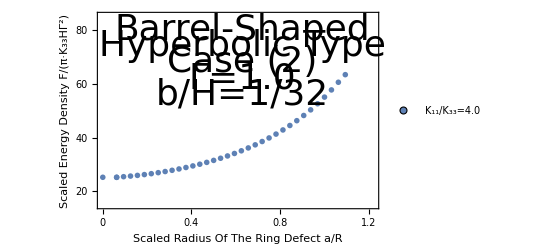

```mathematica
aa=a*Table[{1,4},{i,0,35}];
ListPlot[{aa},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{20,40,60,80},None},{{0,0.2, 0.4, 0.6, 0.8,1,1.2},None}}, PlotRange->{{0,1.22},{15,85}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{0.63,80}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.63,74}],Text[Style["Case (2)",Directive[Black,36]],{0.63,68}],Text[Style["Γ=1.0",Directive[Black,36]],{0.63,62}],Text[Style["b/H=1/32",Directive[Black,36]],{0.63,56}]}]
```